```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

```mathematica
Quantity[3,"Minutes"]
```

3 min

```mathematica
FileSize[$CommandLine[[1]]]
```

48.304 kB

## update

```mathematica
PacletUninstall["CodeParser"]
```

```mathematica
PacletInstall["/Users/brenton/development/stash/COD/codeparser/build/paclet/CodeParser-999.paclet"]
```

PacletObject[CodeParser,999,<>]

```mathematica
PacletDirectoryAdd["/Users/brenton/development/stash/COD/codeparser/build/paclet/CodeParser"];
```

```mathematica
FindFile["CodeParser`"]
```

/Users/brenton/development/stash/COD/ast/build/paclet/AST/Kernel/AST.wl

```mathematica
PacletUpdate["CodeParser","UpdateSites"->True]
```

PacletObject[AST,0.15,<>]

## alphasource Git error

git remote prune origin

git gc --prune=now

git remote prune origin

## build with gcc for -Weffc++ warnings

mkdir build-gcc
cd build-gcc
cmake -DWOLFRAMKERNEL=/Applications/Mathematica110.app/Contents/MacOS/WolframKernel -DCMAKE_CXX_COMPILER=/usr/local/bin/g++-8 -DCMAKE_C_COMPILER=/usr/local/bin/gcc-8 ..
cmake --build . --target paclet

## build with a compilation command database for clang-tidy

mkdir build-clang-tidy
cd build-clang-tidy
cmake -DCMAKE_EXPORT_COMPILE_COMMANDS=ON ..

generates a compile_commands.json in current directory that clang-tidy uses

clang-tidy ByteDecoder.cpp
clang-tidy ByteEncoder.cpp
...

## build for afl fuzzing

Building AFL for the kernel

# build llvm

cd llvm-development
mkdir llvm8
cd llvm8
git clone https://github.com/llvm/llvm-project.git

cd llvm-project/

git fetch
git checkout release/8.x

mkdir build

cd build

cmake -DLLVM_BUILD_LLVM_DYLIB=ON -DLLVM_LINK_LLVM_DYLIB=ON -DLLVM_ENABLE_RTTI=ON -DCMAKE_OSX_DEPLOYMENT_TARGET=10.10 -DCMAKE_INSTALL_PREFIX=install -DLLVM_ENABLE_PROJECTS="clang;libcxx;libcxxabi;lld;compiler-rt" -G "Ninja" ../llvm

ninja
ninja install

# build afl

export CC=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang
export CXX=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang++

cd afl-2.5b
CFLAGS="-mmacosx-version-min=10.10" make

cd llvm-mode
export LLVM_CONFIG=/Users/brenton/development/llvm-development/llvm801/llvm-project/build/install/bin/llvm-config
CFLAGS="-mmacosx-version-min=10.10" make

# build ast

export AFL_CC=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang
export AFL_CXX=/Users/brenton/development/llvm-development/llvm800/llvm-project/build/install/bin/clang++

mkdir build-afl
cd build-afl
cmake -DCMAKE_INSTALL_PREFIX=install -DUSE_MATHLINK=OFF -DBUILD_EXE=ON -DCMAKE_BUILD_TYPE=Debug -DCMAKE_C_COMPILER=/Users/brenton/development/other-development/afl-2.52b/afl-clang-fast  -DCMAKE_CXX_COMPILER=/Users/brenton/development/other-development/afl-2.52b/afl-clang-fast++ ..

cmake --build . --target codeparser-exe

/Users/brenton/development/other-development/afl-2.52b/afl-fuzz -i /Users/brenton/development/stash/COD/codeparser/Tests/files/small -o afl_out/ -x ../Tests/wl.dict cpp/src/exe/codeparser -n -file @@

## build for GCOV

mkdir build-gcc
cd build-gcc

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o API.o -c ../cpp/src/lib/API.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteBuffer.o -c ../cpp/src/lib/ByteBuffer.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteDecoder.o -c ../cpp/src/lib/ByteDecoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o ByteEncoder.o -c ../cpp/src/lib/ByteEncoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CharacterDecoder.o -c ../cpp/src/lib/CharacterDecoder.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Node.o -c ../cpp/src/lib/Node.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Parselet.o -c ../cpp/src/lib/Parselet.cpp 

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Parser.o -c ../cpp/src/lib/Parser.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Source.o -c ../cpp/src/lib/Source.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o SemiSemiParselet.o -c ../cpp/src/lib/SemiSemiParselet.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Tokenizer.o -c ../cpp/src/lib/Tokenizer.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Utils.o -c ../cpp/src/lib/Utils.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o WLCharacter.o -c ../cpp/src/lib/WLCharacter.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CharacterMaps.o -c ../build/generated/cpp/src/lib/CharacterMaps.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Token.o -c ../cpp/src/lib/Token.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o CodePoint.o -c ../build/generated/cpp/src/lib/CodePoint.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o Symbol.o -c ../build/generated/cpp/src/lib/Symbol.cpp

/usr/local/bin/g++-8 --coverage -I ../cpp/include/ -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C -I ../build/generated/cpp/include/ -std=gnu++11 -o TokenEnum.o -c ../build/generated/cpp/src/lib/TokenEnum.cpp


/usr/local/bin/g++-8 --coverage -dynamiclib API.o ByteBuffer.o ByteDecoder.o ByteEncoder.o CharacterDecoder.o Node.o Parselet.o Parser.o SemiSemiParselet.o Source.o Tokenizer.o Utils.o WLCharacter.o CharacterMaps.o Token.o CodePoint.o Symbol.o TokenEnum.o -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -framework mathlink -o AST.dylib


/usr/local/bin/g++-8  -I ../cpp/include -I ../build/generated/cpp/include -I/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I/Applications/Mathematica111.app/Contents/SystemFiles/IncludeFiles/C  --coverage   -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -std=gnu++11 -o main.o -c ../cpp/src/exe/main.cpp


mkdir Frameworks
cd Frameworks
cp -r /Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions/mathlink.framework .
cd ..

mkdir exe
cd exe
/usr/local/bin/g++-8  --coverage ../main.o  -o ast -F/Applications/Mathematica111.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions ../AST.dylib -framework mathlink
cd ..
 
 
exe/ast -file ../Tests/files/carriagereturn.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0003.txt  > /dev/null
exe/ast -file ../Tests/files/inputs-contexts.txt  > /dev/null
exe/ast -file ../Tests/files/inputs-specialchararacters.txt  > /dev/null
exe/ast -file ../Tests/files/linearsyntax.wl > /dev/null
exe/ast -file ../Tests/files/comments.wl > /dev/null
exe/ast -file ../Tests/files/inputs-characternameoperations.txt > /dev/null
exe/ast -file ../Tests/files/inputs-integers.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic.txt > /dev/null
exe/ast -file ../Tests/files/package.wl > /dev/null
exe/ast -file ../Tests/files/crash.txt > /dev/null
exe/ast -file ../Tests/files/inputs-characternames.txt > /dev/null
exe/ast -file ../Tests/files/inputs-nestedsymbolicarithmetic.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic2.txt > /dev/null
exe/ast -file ../Tests/files/sample.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0001.txt > /dev/null
exe/ast -file ../Tests/files/inputs-characternamestrings.txt > /dev/null
exe/ast -file ../Tests/files/inputs-random.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic3.txt > /dev/null
exe/ast -file ../Tests/files/shebangwarning.wl > /dev/null
exe/ast -file ../Tests/files/inputs-0002.txt > /dev/null
exe/ast -file ../Tests/files/inputs-comments.txt > /dev/null
exe/ast -file ../Tests/files/inputs-reals.txt > /dev/null
exe/ast -file ../Tests/files/inputs-symbolicarithmetic4.txt > /dev/null
exe/ast -file ../Tests/files/strange.wl > /dev/null


/usr/local/bin/gcov-8 API.cpp
/usr/local/bin/gcov-8 ByteBuffer.cpp
/usr/local/bin/gcov-8 ByteDecoder.cpp
/usr/local/bin/gcov-8 ByteEncoder.cpp
/usr/local/bin/gcov-8 CharacterDecoder.cpp
/usr/local/bin/gcov-8 Node.cpp
/usr/local/bin/gcov-8 Parselet.cpp
/usr/local/bin/gcov-8 Parser.cpp
/usr/local/bin/gcov-8 SemiSemiParselet.cpp
/usr/local/bin/gcov-8 SyntaxIssue.cpp
/usr/local/bin/gcov-8 Tokenizer.cpp
/usr/local/bin/gcov-8 Utils.cpp
/usr/local/bin/gcov-8 WLCharacter.cpp
/usr/local/bin/gcov-8 CharacterMaps.cpp
/usr/local/bin/gcov-8 Token.cpp
/usr/local/bin/gcov-8 TokenEnum.cpp
/usr/local/bin/gcov-8 CodePoint.cpp
/usr/local/bin/gcov-8 Symbol.cpp

## build for Leak Sanitizing

brenton2maclap:build-leak brenton$ /Users/brenton/development/llvm-development/llvm900/llvm-project/build/install/bin/clang++ -I ../cpp/include -I generated/cpp/include -I /Applications/Mathematica121-6495413.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions -I /Applications/Mathematica110.app/Contents/SystemFiles/IncludeFiles/C -fsanitize=address -g -std=c++11 -L/Applications/Mathematica121-6495413.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions/ -lMLi4 -framework Foundation ../cpp/src/exe/main.cpp ../cpp/src/lib/API.cpp ../cpp/src/lib/ByteDecoder.cpp ../cpp/src/lib/ByteEncoder.cpp ../cpp/src/lib/CharacterDecoder.cpp ../cpp/src/lib/Node.cpp ../cpp/src/lib/Parselet.cpp ../cpp/src/lib/SemiSemiParselet.cpp ../cpp/src/lib/Source.cpp ../cpp/src/lib/SourceManager.cpp ../cpp/src/lib/Token.cpp ../cpp/src/lib/Tokenizer.cpp ../cpp/src/lib/Utils.cpp generated/cpp/src/lib/CodePoint.cpp generated/cpp/src/lib/CharacterMaps.cpp generated/cpp/src/lib/Symbol.cpp ../cpp/src/lib/Parser.cpp ../cpp/src/lib/WLCharacter.cpp generated/cpp/src/lib/TokenEnum.cpp ; ASAN_OPTIONS=detect_leaks=1 ./a.out

## build with GoogleTest

-DGTEST_ROOT=/Users/brenton/development/github-development/googletest/build/install

## Init

```mathematica
$MessagePrePrint=.
```

```mathematica
Needs["CodeParser`"]
```

```mathematica
CodeParser`Private`$Debug=xTrue;
```

```mathematica
xSetSystemOptions["StrictLexicalScoping"->False];
```

```mathematica
installation=$InstallationDirectory<>"/";
```

```mathematica
protos="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/";
```

```mathematica
stash="/Users/brenton/development/stash/";
```

```mathematica
PrependTo[$Path,"/Users/brenton/development/stash/COD/codeparser/Tests/CodeParserTestUtils/"];
```

```mathematica
Needs["CodeParserTestUtils`"]
```

## Init: shims

```mathematica
Needs["AST`"]
```

```mathematica
AST`Shims`Private`setupStackShim[]
```

## Init: setup LongNames

```mathematica
Needs["AST`"]
```

```mathematica
AST`Library`SetupLongNames[]
```

## MExprParser

ANTLR parser history:
https://cvs-master.wolfram.com/viewvc/RD_HTML/TWJ/LocalWork/Parsers/ExprAST/?view=query&branch=&branch_match=exact&dir=&file=&file_match=exact&who=&who_match=exact&comment=&comment_match=exact&querysort=date&hours=2&date=all&mindate=&maxdate=&limit_changes=

https://stash.wolfram.com/projects/JAVA/repos/mexprparser/commits

## other parsers

https://github.com/mathics/Mathics/tree/master/mathics/core/parser

https://github.com/rljacobson/FoxySheep

https://github.com/halirutan/Wolfram-Language-Parser

https://gitlab.com/cznic/wl

## other links

https://www.robertjacobson.dev/defining-the-wolfram-language-part-1-finding-operators

## test a single file

```mathematica
Quit[]
```

```mathematica
Needs["AST`"]
```

```mathematica
file="/Users/brenton/development/stash/COD/ast/build/test.m";
```

```mathematica
file="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/CompileUtilities/CompileUtilities/RuntimeChecks/RuntimeChecks.m";
```

```mathematica
Head[file]
```

String

```mathematica
FileByteCount[file]
```

9

```mathematica
actualCST=ConcreteParseFile[file,HoldNode[Hold,#[[1]],<||>]&];
```

```mathematica
If[!FreeQ[actualCST,_SyntaxErrorNode],
Print["has errors"]
]
```

```mathematica
actualAgg=AST`Abstract`Aggregate[actualCST];
```

```mathematica
tryString=ToInputFormString[actualAgg];
If[!StringQ[tryString],
Print["tryString is not a String"];
]
```

```mathematica
If[!FreeQ[actualAgg,LeafNode[Symbol,"Package",_]],
tryString=StringReplace[tryString,"Package"->"PackageXXX"];
]
```

```mathematica
actual=DeleteCases[ToExpression[tryString,InputForm],Null];
```

```mathematica
(text=FromCharacterCode[Import[file,"Byte"],"UTF8"])//FullForm;
```

```mathematica
If[!FreeQ[actualCST,LeafNode[Symbol,"Package",_]],
text=StringReplace[text,"Package"->"PackageXXX"];
]
```

```mathematica
expected=DeleteCases[ToExpression[text,InputForm,Hold],Null];//AbsoluteTiming
```

{0.00001,Null}

```mathematica
actual===expected
```

True

```mathematica
(* Abstract *)
actualAST=AST`Abstract`Abstract[actualAgg];
```

```mathematica
tryString=ToFullFormString[actualAST];
If[!StringQ[tryString],
Print[tryString];
Quit[]
]
```

```mathematica
If[!FreeQ[actualAST,LeafNode[Symbol,"Package",_]],
tryString=StringReplace[tryString,"Package"->"PackageXXX"];
]
```

```mathematica
actual=DeleteCases[ToExpression[tryString,InputForm],Null];
```

```mathematica
actual===expected
```

True

```mathematica
expected=$LastFailedExpected;
```

```mathematica
actual=$LastFailedActual;
```

```mathematica
Length[expected]
```

5

```mathematica
Length[actual]
```

5

```mathematica
Position[Table[Extract[expected,{i},Hold]===Extract[actual,{i},Hold],{i,1,Min[Length[actual],Length[expected]]}],False]
```

{{2},{4}}

```mathematica
spec={2};
a=Extract[expected,spec,Hold]//FullForm
b=Extract[actual,spec,Hold]//FullForm
a===b
```

Hold[CompoundExpression[Begin["`Private`"],Null]]

Hold[Begin["`Private`"]]

False

```mathematica
Do[
Pause[0.01];
spec={66,1,2,2,i};
a=Extract[expected,spec,Hold];
b=Extract[actual,spec,Hold];
If[a=!=b,Print[i];Break[]]
,
{i,1,10000}
]
```

6

```mathematica
FilePrint[file]
```

PacletManager`Package`getPacletWithProgress["AstronomyConvenienceFunctions"];



Get["AstronomyConvenienceFunctions`"]

## test all files

```mathematica
prefix:=stash<>"QA/";
prefix:=protos;
prefix:="/Users/brenton/development/github-development/";
prefix=stash<>"KERN/Kernel/StartUp/";
names1:=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"(*"*.nb"*),prefix,Infinity];
names2:=FileNames["*.nb",prefix,Infinity];
names=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"|"*.wls",prefix,Infinity];

toDelete=Select[names,StringContainsQ[#,".git"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CMake"]&];
names=Complement[names,toDelete];

(*
Directory, not a file
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"neuralnetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];

(*
weird
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"system/InputOutput/Get/corruptedprefs.m"]];
names=Complement[names,toDelete];
```

1827

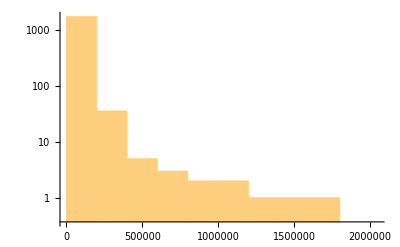

```mathematica
Length[names]
Histogram[FileByteCount/@names,100,ScalingFunctions->"Log"]
```

```mathematica
$ProcessID
```

27493

```mathematica
$DebugLoop=xTrue;
$visuals=xTrue;
```

```mathematica
CodeParserTestUtils`Private`$DebugTopLevelExpressions=xTrue;
```

```mathematica
$minSizeLimit=0.00*^6;
$maxSizeLimit=5.00*^6;
```

```mathematica
start=1;
```

```mathematica
x=start;
file=None;
Print["Parsing ", Length[names[[start;;]]]," files"];
Print["Current file: ",Dynamic[Short[file]]];
Print["Current file size: ",Dynamic[FileSize[file]]];
If[$visuals,
Print["Current file bytes/s: ",Dynamic[bytesPerSecond]]
];
Print["Current index: ",Dynamic[x]];
If[$visuals,
Print[Grid[{
{"concrete",Dynamic[CodeParser`Library`$ConcreteParseTime],ProgressIndicator[Dynamic[CodeParser`Library`$ConcreteParseProgress],{0,100}]},
{"aggregate",Dynamic[CodeParser`Abstract`$AggregateParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AggregateParseProgress],{0,100}]},
{"abstract",Dynamic[CodeParser`Abstract`$AbstractParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AbstractParseProgress],{0,100}]},
{"","",Dynamic[PieChart[{CodeParser`Library`$ConcreteParseTime,CodeParser`Abstract`$AggregateParseTime,CodeParser`Abstract`$AbstractParseTime},ImageSize->Tiny,ChartLegends->{"concrete","aggregate","abstract"}]]}
},Alignment->Right]];
];
Print[Row[{"overall",Spacer[10],ProgressIndicator[Dynamic[x],{0,Length[names]}]}]];
Scan[(
file=#;

Which[
TrueQ[$DebugLoop],
Print[x," ",file]
,
Mod[x,100]==0,
Print[x," ",file];
NotebookSave[EvaluationNotebook[]]
];

CodeParser`Library`$ConcreteParseProgress=Quantity[0,"Seconds"];
CodeParser`Abstract`$AggregateParseProgress=Quantity[0,"Seconds"];
CodeParser`Abstract`$AbstractParseProgress=Quantity[0,"Seconds"];
CodeParser`Library`$ConcreteParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AggregateParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AbstractParseTime=Quantity[0,"Seconds"];
bytesPerSecond=0;
res=CodeParserTestUtils`parseTest[#,x,"FileNamePrefixPattern"->prefix,"FileSizeLimit"->{$minSizeLimit,$maxSizeLimit}];
(*implicitTimesTest[file,x,"FileNamePrefixPattern"->prefix];*)
If[res=!=ok,
If[$visuals,
bytesPerSecond=FileSize[file]/(CodeParser`Library`$ConcreteParseTime);
Pause[2.0];
];
];
x++;
)&
,
names[[start;;]]
]//AbsoluteTiming
```

Parsing 1827 files

Current file:

Current file size:

Current index:

overall

100 /Users/brenton/development/stash/KERN/Kernel/StartUp/Control/BodePlots.m

200 /Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/HDF.m

300 /Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/Utilities.m

$Aborted

## test Boxes from WolframLanguageData Documentation Examples

```mathematica
Quit[]
```

```mathematica
Needs["AST`"]
```

```mathematica
names=Names["System`*"];
```

```mathematica
$Debug=xTrue;
$visuals=True;
```

```mathematica
$MessagePrePrint=.
```

```mathematica
If[$visuals,
Print[Dynamic[{name,nn}]];
Print[ProgressIndicator[Dynamic[nn],{1,Length[names]}]]
]
```

```mathematica
start=1;
```

```mathematica
Get["/Users/brenton/development/stash/COD/ast/Tests/ASTTestUtils/Boxes.wl"]
```

```mathematica
Do[
nn=n;
name=names[[n]];
Which[
TrueQ[$Debug],
Print[{n,name}]
,
Mod[n,100]==0,
Print[{n,name}];
NotebookSave[EvaluationNotebook[]];
];

examples=WolframLanguageData[name,"DocumentationBasicExamples"];
Do[
If[$Debug,
Print["i: ",i];
];
example=examples[[i]];
boxes=Flatten[Cases[example,RawBoxes[Cell[BoxData[box_],___]]:>box,2]];
Do[
If[$Debug,
Print["j: ",j];
];
box=boxes[[j]];
If[$Debug&&xTrue,
Print["box: ",box//InputForm];
];
res=parseBoxTest[box,name,n,i,j];
If[res===continue,Continue[]];
If[res=!=Null,Throw[res]],
{j,1,Length[boxes]}
];
,
{i,1,Length[examples]}
]
,
{n,start,Length[names]}
]
```

{100,ψ}

$Aborted

## test Boxes from Documentation Notebooks

```mathematica
Needs["CodeParser`"]
```

```mathematica
Get["/Users/brenton/development/stash/COD/codeparser/Tests/CodeParserTestUtils/Boxes.wl"]
```

```mathematica
names=FileNames["*.nb",$InstallationDirectory,Infinity];
```

```mathematica
Clear[descendToInputCells]
descendToInputCells[Notebook[cells_List,___]]:=descendToInputCells/@cells;
descendToInputCells[Cell[_String,_,___]]:=Null
descendToInputCells[Cell[TextData[___],_,___]]:=Null
descendToInputCells[Cell[GraphicsData[___],_,___]]:=Null
descendToInputCells[Cell[CellGroupData[cells_List,_],___]]:=descendToInputCells/@cells
descendToInputCells[Cell[BoxData[box_],"Input",___]]:=Print[parseBoxTest[box,"foo",1,2,3]]
descendToInputCells[Cell[BoxData[box_],_,___]]:=Null
descendToInputCells[args___]:=Throw[{"cannot descend",{args}}]
```

```mathematica
name=RandomChoice[names]
```

/Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/JLink/Documentation/English/Tutorials/CallingJavaFromTheWolframLanguage.nb

```mathematica
NotebookOpen[name,Visible->False]
```

msfbj_shm131FrontEndObject[LinkObject["msfbj_shm", 3, 1]]131Calling Java from the Wolfram Language/Applications/Mathematica121-6670671.app/Contents/SystemFiles/Links/JLink/Documentation/English/Tutorials/CallingJavaFromTheWolframLanguage.nb

```mathematica
nb=NotebookGet[%];
```

```mathematica
descendToInputCells[nb];
```

Null

Null

Null

«8 more identical outputs»

from boxes:  {InfixNode[Times,{InfixNode[CompoundExpression,{BinaryNode[BinaryAt,{LeafNode[Symbol,obj,<||>],LeafNode[Token`At,@,<||>],CallNode[LeafNode[Symbol,method,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,args,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>],LeafNode[Token`Fake`ImplicitTimes,,<||>],InfixNode[CompoundExpression,{CallNode[LeafNode[Symbol,obj,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],CallNode[LeafNode[Symbol,method,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,args,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>]},<||>]}
from string: {InfixNode[CompoundExpression,{BinaryNode[BinaryAt,{LeafNode[Symbol,obj,<||>],LeafNode[Token`At,@,<||>],CallNode[LeafNode[Symbol,method,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,args,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],CallNode[LeafNode[Symbol,obj,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],CallNode[LeafNode[Symbol,method,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,args,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>]}

{comparing aggs,foo,1,2,3}

from boxes:  {InfixNode[Times,{InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,x,<||>],LeafNode[Token`Equal,=,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,obj,<||>],LeafNode[Token`At,@,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,field,<||>],LeafNode[Token`At,@,<||>],CallNode[LeafNode[Symbol,method,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,args,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>],LeafNode[Token`Fake`ImplicitTimes,,<||>],InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,x,<||>],LeafNode[Token`Equal,=,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,obj,<||>],LeafNode[Token`At,@,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,field1,<||>],LeafNode[Token`At,@,<||>],LeafNode[Symbol,field2,<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>]},<||>]}
from string: {InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,x,<||>],LeafNode[Token`Equal,=,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,obj,<||>],LeafNode[Token`At,@,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,field,<||>],LeafNode[Token`At,@,<||>],CallNode[LeafNode[Symbol,method,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,args,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],BinaryNode[Set,{LeafNode[Symbol,x,<||>],LeafNode[Token`Equal,=,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,obj,<||>],LeafNode[Token`At,@,<||>],BinaryNode[BinaryAt,{LeafNode[Symbol,field1,<||>],LeafNode[Token`At,@,<||>],LeafNode[Symbol,field2,<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>]}

{comparing aggs,foo,1,2,3}

Null

Null

Null

continue

continue

Null

Null

Null

«4 more identical outputs»

{concrete,{Length,ToStandardFormBoxes[ContainerNode[Box,{InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,urlClass,<|Source→{1,1,1,1,1}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{1,1,1,1,2}|>],LeafNode[Token`Equal,=,<|Source→{1,1,1,1,3}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{1,1,1,1,4}|>],CallNode[{LeafNode[Symbol,LoadJavaClass,<|Source→{1,1,1,1,5,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{1,1,1,1,5,1,2}|>],LeafNode[String,"java.net.URL",<|Source→{1,1,1,1,5,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{1,1,1,1,5,1,4}|>]},<||>]},<|Source→{1,1,1,1,5,1}|>]},<|Source→{1,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{1,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{1,1,2}|>]},<|Source→{1,1}|>],LeafNode[Token`Newline,
,<|Source→{2}|>],BoxNode[RowBox,{{InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,urlObject,<|Source→{3,1,1,1,1,1,1}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,1,1,1,1,2}|>],LeafNode[Token`Equal,=,<|Source→{3,1,1,1,1,1,3}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,1,1,1,1,4}|>],CallNode[{LeafNode[Symbol,JavaNew,<|Source→{3,1,1,1,1,1,5,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{3,1,1,1,1,1,5,1,2}|>],InfixNode[Comma,{LeafNode[String,"java.net.URL",<|Source→{3,1,1,1,1,1,5,1,3,1,1}|>],LeafNode[Token`Comma,,,<|Source→{3,1,1,1,1,1,5,1,3,1,2}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,1,1,1,1,5,1,3,1,3}|>],LeafNode[String,"http://www.wolfram.com",<|Source→{3,1,1,1,1,1,5,1,3,1,4}|>]},<|Source→{3,1,1,1,1,1,5,1,3,1}|>],LeafNode[Token`CloseSquare,],<|Source→{3,1,1,1,1,1,5,1,4}|>]},<||>]},<|Source→{3,1,1,1,1,1,5,1}|>]},<|Source→{3,1,1,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{3,1,1,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{3,1,1,1,2}|>]},<|Source→{3,1,1,1}|>],LeafNode[Token`Newline,
,<|Source→{3,1,2}|>],GroupNode[Comment,{LeafNode[Token`Boxes`OpenParenStar,(*,<|Source→{3,1,3,1,1}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,2}|>],InfixNode[Times,{LeafNode[Symbol,The,<|Source→{3,1,3,1,3,1,1}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,3,1,2}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{3,1,3,1,3,1,3}|>],LeafNode[Symbol,next,<|Source→{3,1,3,1,3,1,3}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,3,1,4}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{3,1,3,1,3,1,5}|>],LeafNode[Symbol,three,<|Source→{3,1,3,1,3,1,5}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,3,1,6}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{3,1,3,1,3,1,7}|>],LeafNode[Symbol,lines,<|Source→{3,1,3,1,3,1,7}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,3,1,8}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{3,1,3,1,3,1,9}|>],LeafNode[Symbol,are,<|Source→{3,1,3,1,3,1,9}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,3,1,10}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{3,1,3,1,3,1,11}|>],LeafNode[Symbol,equivalent,<|Source→{3,1,3,1,3,1,11}|>]},<|Source→{3,1,3,1,3,1}|>],LeafNode[Token`Boxes`MultiWhitespace, ,<|Source→{3,1,3,1,4}|>],LeafNode[Token`Boxes`StarCloseParen,*),<|Source→{3,1,3,1,5}|>]},<|Source→{3,1,3,1}|>]}},<|Source→{3}|>],LeafNode[Token`Newline,
,<|Source→{4}|>],CallNode[{LeafNode[Symbol,Methods,<|Source→{5,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{5,1,2}|>],LeafNode[Symbol,urlClass,<|Source→{5,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{5,1,4}|>]},<||>]},<|Source→{5,1}|>],LeafNode[Token`Newline,
,<|Source→{6}|>],CallNode[{LeafNode[Symbol,Methods,<|Source→{7,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{7,1,2}|>],LeafNode[Symbol,urlObject,<|Source→{7,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{7,1,4}|>]},<||>]},<|Source→{7,1}|>],LeafNode[Token`Newline,
,<|Source→{8}|>],CallNode[{LeafNode[Symbol,Methods,<|Source→{9,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{9,1,2}|>],LeafNode[String,"java.net.URL",<|Source→{9,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{9,1,4}|>]},<||>]},<|Source→{9,1}|>]},<||>]]},{foo,1,2,3}}

Null

Null

Null

«12 more identical outputs»

continue

continue

continue

«1 more identical outputs»

Null

Null

Null

«7 more identical outputs»

from boxes:  {BinaryNode[SetDelayed,{CallNode[LeafNode[Symbol,MyFunc,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],PatternBlankSequenceNode[PatternBlankSequence,{LeafNode[Symbol,args,<||>],LeafNode[BlankSequence,__,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`ColonEqual,:=,<||>],CallNode[LeafNode[Symbol,JavaBlock,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],CallNode[LeafNode[Symbol,Module,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],LeafNode[Symbol,locals,<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Token`DotDotDot,...,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]}
from string: {BinaryNode[SetDelayed,{CallNode[LeafNode[Symbol,MyFunc,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],PatternBlankSequenceNode[PatternBlankSequence,{LeafNode[Symbol,args,<||>],LeafNode[BlankSequence,__,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`ColonEqual,:=,<||>],CallNode[LeafNode[Symbol,JavaBlock,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],CallNode[LeafNode[Symbol,Module,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],PostfixNode[RepeatedNull,{InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],LeafNode[Symbol,locals,<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>],LeafNode[Token`DotDotDot,...,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]}

{comparing aggs,foo,1,2,3}

from boxes:  {BinaryNode[SetDelayed,{CallNode[LeafNode[Symbol,MyOtherFunc,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],PatternBlankSequenceNode[PatternBlankSequence,{LeafNode[Symbol,args,<||>],LeafNode[BlankSequence,__,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`ColonEqual,:=,<||>],CallNode[LeafNode[Symbol,JavaBlock,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],CallNode[LeafNode[Symbol,Module,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],LeafNode[Symbol,obj,<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],InfixNode[Times,{PostfixNode[RepeatedNull,{InfixNode[CompoundExpression,{BinaryNode[Set,{InfixNode[Times,{LeafNode[Token`DotDotDot,...,<||>],LeafNode[Token`Fake`ImplicitTimes,,<||>],LeafNode[Symbol,obj,<||>]},<||>],LeafNode[Token`Equal,=,<||>],CallNode[LeafNode[Symbol,JavaNew,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[String,"java.awt.Frame",<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>],LeafNode[Token`DotDotDot,...,<||>]},<||>],LeafNode[Token`Fake`ImplicitTimes,,<||>],CallNode[LeafNode[Symbol,Return,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,obj,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]}
from string: {BinaryNode[SetDelayed,{CallNode[LeafNode[Symbol,MyOtherFunc,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],PatternBlankSequenceNode[PatternBlankSequence,{LeafNode[Symbol,args,<||>],LeafNode[BlankSequence,__,<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`ColonEqual,:=,<||>],CallNode[LeafNode[Symbol,JavaBlock,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],CallNode[LeafNode[Symbol,Module,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],InfixNode[Times,{PostfixNode[RepeatedNull,{InfixNode[CompoundExpression,{BinaryNode[Set,{InfixNode[Times,{PostfixNode[RepeatedNull,{InfixNode[Comma,{GroupNode[List,{LeafNode[Token`OpenCurly,{,<||>],LeafNode[Symbol,obj,<||>],LeafNode[Token`CloseCurly,},<||>]},<||>],LeafNode[Token`Comma,,,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>],LeafNode[Token`DotDotDot,...,<||>]},<||>],LeafNode[Token`Fake`ImplicitTimes,,<||>],LeafNode[Symbol,obj,<||>]},<||>],LeafNode[Token`Equal,=,<||>],CallNode[LeafNode[Symbol,JavaNew,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[String,"java.awt.Frame",<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`Semi,;,<||>],LeafNode[Token`Fake`ImplicitNull,,<||>]},<||>],LeafNode[Token`DotDotDot,...,<||>]},<||>],LeafNode[Token`Fake`ImplicitTimes,,<||>],CallNode[LeafNode[Symbol,Return,<||>],{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<||>],LeafNode[Symbol,obj,<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>],LeafNode[Token`CloseSquare,],<||>]},<||>]},<||>]},<||>]}

{comparing aggs,foo,1,2,3}

Null

Null

Null

«25 more identical outputs»

{concrete,{Length,ToStandardFormBoxes[ContainerNode[Box,{BoxNode[RowBox,{{InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,frm,<|Source→{1,1,1,1,1,1,1}|>],LeafNode[Token`Equal,=,<|Source→{1,1,1,1,1,1,2}|>],CallNode[{LeafNode[Symbol,JavaNew,<|Source→{1,1,1,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{1,1,1,1,1,1,3,1,2}|>],LeafNode[String,"com.wolfram.jlink.MathFrame",<|Source→{1,1,1,1,1,1,3,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{1,1,1,1,1,1,3,1,4}|>]},<||>]},<|Source→{1,1,1,1,1,1,3,1}|>]},<|Source→{1,1,1,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{1,1,1,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{1,1,1,1,2}|>]},<|Source→{1,1,1,1}|>],LeafNode[Token`Newline,
,<|Source→{1,1,2}|>]}},<|Source→{1}|>],LeafNode[Token`Newline,
,<|Source→{2}|>],InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,button,<|Source→{3,1,1,1,1}|>],LeafNode[Token`Equal,=,<|Source→{3,1,1,1,2}|>],CallNode[{LeafNode[Symbol,JavaNew,<|Source→{3,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{3,1,1,1,3,1,2}|>],LeafNode[String,"java.awt.Button",<|Source→{3,1,1,1,3,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{3,1,1,1,3,1,4}|>]},<||>]},<|Source→{3,1,1,1,3,1}|>]},<|Source→{3,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{3,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{3,1,2}|>]},<|Source→{3,1}|>],LeafNode[Token`Newline,
,<|Source→{4}|>],BoxNode[RowBox,{{InfixNode[CompoundExpression,{BinaryNode[Set,{LeafNode[Symbol,textField,<|Source→{5,1,1,1,1,1,1}|>],LeafNode[Token`Equal,=,<|Source→{5,1,1,1,1,1,2}|>],CallNode[{LeafNode[Symbol,JavaNew,<|Source→{5,1,1,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{5,1,1,1,1,1,3,1,2}|>],LeafNode[String,"java.awt.TextField",<|Source→{5,1,1,1,1,1,3,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{5,1,1,1,1,1,3,1,4}|>]},<||>]},<|Source→{5,1,1,1,1,1,3,1}|>]},<|Source→{5,1,1,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{5,1,1,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{5,1,1,1,2}|>]},<|Source→{5,1,1,1}|>],LeafNode[Token`Newline,
,<|Source→{5,1,2}|>]}},<|Source→{5}|>],LeafNode[Token`Newline,
,<|Source→{6}|>],InfixNode[CompoundExpression,{BinaryNode[BinaryAt,{LeafNode[Symbol,frm,<|Source→{7,1,1,1,1}|>],LeafNode[Token`At,@,<|Source→{7,1,1,1,2}|>],CallNode[{LeafNode[Symbol,setLayout,<|Source→{7,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{7,1,1,1,3,1,2}|>],CallNode[{LeafNode[Symbol,JavaNew,<|Source→{7,1,1,1,3,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{7,1,1,1,3,1,3,1,2}|>],LeafNode[String,"java.awt.GridLayout",<|Source→{7,1,1,1,3,1,3,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{7,1,1,1,3,1,3,1,4}|>]},<||>]},<|Source→{7,1,1,1,3,1,3,1}|>],LeafNode[Token`CloseSquare,],<|Source→{7,1,1,1,3,1,4}|>]},<||>]},<|Source→{7,1,1,1,3,1}|>]},<|Source→{7,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{7,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{7,1,2}|>]},<|Source→{7,1}|>],LeafNode[Token`Newline,
,<|Source→{8}|>],InfixNode[CompoundExpression,{BinaryNode[BinaryAt,{LeafNode[Symbol,frm,<|Source→{9,1,1,1,1}|>],LeafNode[Token`At,@,<|Source→{9,1,1,1,2}|>],CallNode[{LeafNode[Symbol,add,<|Source→{9,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{9,1,1,1,3,1,2}|>],LeafNode[Symbol,button,<|Source→{9,1,1,1,3,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{9,1,1,1,3,1,4}|>]},<||>]},<|Source→{9,1,1,1,3,1}|>]},<|Source→{9,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{9,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{9,1,2}|>]},<|Source→{9,1}|>],LeafNode[Token`Newline,
,<|Source→{10}|>],InfixNode[CompoundExpression,{BinaryNode[BinaryAt,{LeafNode[Symbol,frm,<|Source→{11,1,1,1,1}|>],LeafNode[Token`At,@,<|Source→{11,1,1,1,2}|>],CallNode[{LeafNode[Symbol,add,<|Source→{11,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{11,1,1,1,3,1,2}|>],LeafNode[Symbol,textField,<|Source→{11,1,1,1,3,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{11,1,1,1,3,1,4}|>]},<||>]},<|Source→{11,1,1,1,3,1}|>]},<|Source→{11,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{11,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{11,1,2}|>]},<|Source→{11,1}|>],LeafNode[Token`Newline,
,<|Source→{12}|>],InfixNode[CompoundExpression,{BinaryNode[BinaryAt,{LeafNode[Symbol,frm,<|Source→{13,1,1,1,1}|>],LeafNode[Token`At,@,<|Source→{13,1,1,1,2}|>],CallNode[{LeafNode[Symbol,pack,<|Source→{13,1,1,1,3,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{13,1,1,1,3,1,2}|>],LeafNode[Token`CloseSquare,],<|Source→{13,1,1,1,3,1,3}|>]},<||>]},<|Source→{13,1,1,1,3,1}|>]},<|Source→{13,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{13,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{13,1,2}|>]},<|Source→{13,1}|>],LeafNode[Token`Newline,
,<|Source→{14}|>],InfixNode[CompoundExpression,{CallNode[{LeafNode[Symbol,JavaShow,<|Source→{15,1,1,1,1}|>]},{GroupNode[GroupSquare,{LeafNode[Token`OpenSquare,[,<|Source→{15,1,1,1,2}|>],LeafNode[Symbol,frm,<|Source→{15,1,1,1,3}|>],LeafNode[Token`CloseSquare,],<|Source→{15,1,1,1,4}|>]},<||>]},<|Source→{15,1,1,1}|>],LeafNode[Token`Semi,;,<|Source→{15,1,2}|>],LeafNode[Token`Fake`ImplicitNull,,<|Source→{15,1,2}|>]},<|Source→{15,1}|>]},<||>]]},{foo,1,2,3}}

Null

Null

Null

«38 more identical outputs»

continue

continue

continue

«2 more identical outputs»

## random string testing

```mathematica
Needs["AST`"]
```

```mathematica
$ProcessID
```

18523

```mathematica
get=Get["/Users/brenton/development/stash/COD/ast/tables/LongNames.wl"];
```

```mathematica
punct=Select[get,#==PunctuationCharacter&];
```

```mathematica
raw=Select[get,#==RawCharacter&];
```

```mathematica
unsupported=Select[get,#==UnsupportedCharacter&];
```

```mathematica
punctNames=Keys[punct];
```

```mathematica
rawNames=Keys[raw];
```

```mathematica
unsupportedNames=Keys[unsupported];
```

```mathematica
names=punctNames;
```

```mathematica
names=Complement[names,rawNames];
```

```mathematica
names=Complement[names,unsupportedNames];
```

```mathematica
dontBother={"InvisibleComma","Integral","ContourIntegral","DoubleContourIntegral","ClockwiseContourIntegral","CounterClockwiseContourIntegral"};
names=Complement[names,dontBother];
```

```mathematica
buggy={"ImplicitPlus",
"Star",
"Coproduct",
"LeftDoubleBracket",
"DiscretionaryParagraphSeparator",
"DiscretionaryLineSeparator"};
buggy={};
```

```mathematica
parseToSymbols={"Infinity",
"ImaginaryI",
"Pi",
"ImaginaryJ",
"Degree",
"ExponentialE"};
parseToSymbols={};
```

```mathematica
names=Complement[names,buggy];
```

```mathematica
names=Complement[names,parseToSymbols];
```

```mathematica
names//Length
```

298

```mathematica
tabProb=0;
newlineProb=0;
spaceProb=0;
punctProb=0;
```

```mathematica
rules=Rule@@Transpose[{{tabProb,"\t"},{newlineProb,"\n"},{0," "},{0,"!"},{0,"\""},{0,"#"},{0,"$"},{0,"%"},{0,"&"},{0,"'"},{0,"("},{0,")"},{1,"*"},{1,"+"},{0,","},{1,"-"},{1,"."},{0,"/"},{1,"1"},{2,"1"},{3,"1"},
{0,":"},{0,";"},{0,"<"},{0,"="},{0,">"},{0,"?"},{0,"@"},
{0,"A"},
{0,"["},
{0,"\\"},
{0,"]"},
{1,"^"},
{0,"_"},{1,"`"},{0,"{"},{0,"|"},{0,"}"},{0,"~"}}~Join~(({0,"\\["<>#<>"]"})&/@names)];
```

### test

```mathematica
$ProcessID
```

18523

bug 382766: a . -b cannot be parsed
bug 385771: Inequality (Greater, Less, etc.) operators are absorbed by VectorInequality operators
bug 385777: Parsing \ [Star] and implicit Times is buggy
bug 385784: Context (with no symbol) is silently truncated from RHS of _
bug 365287: ImplicitPlus

```mathematica
bothFailed=0;
bothSucceeded=0;
bug385771=0;
bug385777=0;
bug382766=0;
bug385784=0;
stringification=0;
bug365287=0;
toReport1=0;
toReport2=0;
bad=0;
badStrs={};
```

```mathematica
Print[Grid[{
{"bothFailed",Dynamic[bothFailed]},
{"bothSucceeded",Dynamic[bothSucceeded]},
{"bug385771",Dynamic[bug385771]},
{"bug385777",Dynamic[bug385777]},
{"bug382766",Dynamic[bug382766]},
{"bug385784",Dynamic[bug385784]},
{"stringification",Dynamic[stringification]},
{"bug365287",Dynamic[bug365287]},
{"toReport1",Dynamic[toReport1]},
{"toReport2",Dynamic[toReport2]},
{"bad",Dynamic[bad]},
{"","",Dynamic[PieChart[{Log[bothFailed],Log[bothSucceeded],Log[bug385771],Log[bug385777],Log[bug382766],Log[bug385784],Log[stringification],Log[bug365287],Log[toReport1],Log[toReport2],Log[bad]},ImageSize->Tiny,ChartLegends->{"bothFailed","bothSucceeded","bug385771","bug385777","bug382766","bug385784","stringification","bug365287","toReport1","toReport2","bad"}]]}
},Alignment->Right]]
```

bothFailed |  | 
bothSucceeded |  | 
bug385771 |  | 
bug385777 |  | 
bug382766 |  | 
bug385784 |  | 
stringification |  | 
bug365287 |  | 
toReport1 |  | 
toReport2 |  | 
bad |  | 
 |  |

```mathematica
Print[Dynamic[str]]
```

```mathematica
While[True,
Pause[0.0];

str=StringJoin[RandomChoice[rules,15]];

str >> "/Users/brenton/development/stash/COD/ast/build/test.m";

expr=Quiet[ToExpression[str,InputForm,Hold]];

If[expr===$Failed,

test=ParseString[str,ContainerNode[Hold,#[[1]],<||>]&];

(*If[!FreeQ[test,CallNode[LeafNode[Symbol,"Dot",_],{___,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus"|"Not"|"Span",_],_,_]|
PrefixNode[Minus,{LeafNode[Token`Minus,"-",_],_},_]},_]|
CallNode[LeafNode[Symbol,"Put"|"Get",_],_,_]],Continue[]];*)

testStr=ToFullFormString[test];

If[StringQ[testStr],
If[!StringFreeQ[testStr,"AST`Comma"],
comma++;
testStr=Failure["CommaFailure",<||>];
];
];

If[!FailureQ[testStr],

If[!FreeQ[test,CallNode[LeafNode[Symbol,"Dot",_],{___,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus"|"Not"|"Span",_],_,_]|
PrefixNode[Minus|PreIncrement,_,_]|
LeafNode[Real|Integer,s_/;StringStartsQ[s,"-"],_]},_]],bug382766++;Continue[]];

If[!FreeQ[test,CallNode[LeafNode[Symbol,"Put"|"Get",_],_,_]],stringification++;Continue[]];

If[!FreeQ[test,PostfixNode[Repeated,{LeafNode[Integer,s_/;StringContainsQ[s,"^^"],_],LeafNode[Token`DotDot,"..",_]},_]],
toReport2++;Continue[]
];

xPrint["ToExpression failed; CodeTools succeeded"];
fullFormStr=$Failed;

bad++;
AppendTo[badStrs,str];

Continue[]
];

bothFailed++;
Continue[]
];

If[!FreeQ[expr,Information,Infinity,Heads->True],
information++;
Continue[]
];

(*If[!FreeQ[expr,_Real,Infinity,Heads->True],Continue[]];*)

(*If[!FreeQ[expr,Get|MessageName|Put|PutAppend,Infinity,Heads->True],Continue[]];*)

(*If[!FreeQ[expr,Null,Infinity,Heads->True],Continue[]];*)

fullFormStr=ToString[FullForm[expr]];

(*If[!StringFreeQ[fullFormStr,"\\\\"],Continue[]];*)

If[!StringFreeQ[fullFormStr,"Developer`VectorInequality"],bug385771++;Continue[]];

test=ParseString[str,ContainerNode[Hold,#[[1]],<||>]&];

(*If[!FreeQ[test,(*CallNode[LeafNode[Symbol,"Dot",_],{_,
CallNode[LeafNode[Symbol,"Times",_],{LeafNode[Integer,"-1",_],_},_]|
CallNode[LeafNode[Symbol,"Plus",_],_,_]|
PrefixNode[Minus,{LeafNode[Token`Minus,"-",_],_},_]|
CallNode[LeafNode[Symbol,"Not",_],_,_]},_]|*)
LeafNode[Token`QuestionQuestion,"??",_]],Continue[]];*)

(*
reals can print differently:
.8 vs. 0.8, etc.

symbols can print differently:
`a vs. a

integers can print differently: 0123
*)
testStr=ToFullFormString[test/.{
LeafNode[Real,r_,data_]:>LeafNode[Real,ToString[FullForm[ToExpression[r]]],data],
LeafNode[Integer,i_,data_]:>LeafNode[Integer,ToString[FullForm[ToExpression[i]]],data],
LeafNode[Symbol,s_,data_]:>LeafNode[Symbol,ToExpression[s,InputForm,Function[xx,ToString[Unevaluated[xx],InputForm],{HoldFirst}]],data]}];

If[FailureQ[testStr],

cst=ConcreteParseString[str];

If[!FreeQ[cst,
PatternBlankNode[PatternBlank,{_,_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]|
BlankNode[Blank,{_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]|
BlankSequenceNode[BlankSequence,{_,LeafNode[Token`Error`ExpectedLetterlike,_,_]},_]],
bug385784++;
Continue[]
];

If[!FreeQ[cst,
InfixNode[Plus,{
LeafNode[Real,s_/;StringMatchQ[s,___~~"`"],_]|InfixNode[Times,{___,LeafNode[Real,s_/;StringMatchQ[s,___~~"`"],_]},_]
,
LeafNode[Token`Minus|Token`Plus,_,_],InfixNode[Times,{ErrorNode[Token`Error`ExpectedOperand,_,_],LeafNode[Token`Star,"*",_],___},_]},_]],
toReport1++;
Continue[]
];

xPrint["ToExpression succeeded; CodeTools failed"];

bad++;
AppendTo[badStrs,str];

Continue[]
];

(*If[!StringFreeQ[testStr,"\\<"|"\\>"|"\\ "],Continue[]];*)

If[testStr=!=fullFormStr,

cst=ConcreteParseString[str];

If[!FreeQ[cst,InfixNode[Star,{___,InfixNode[Times,{___,LeafNode[Token`Fake`ImplicitTimes,_,_],___},_],___},_]],
bug385777++;
Continue[]
];

If[!FreeQ[cst,LeafNode[Token`LongName`ImplicitPlus,_,_]],
bug365287++;
Continue[]
];

xPrint["exprs succeeded, but differ"];

bad++;
AppendTo[badStrs,str];

Continue[];
];

bothSucceeded++;
]
```

$Aborted

### examine

```mathematica
badStrs
```

{1`*1111`1*11^^.}

```mathematica
1-*2
```

```mathematica
11
```

11

```mathematica
Quit[]
```

```mathematica
1
```

1

```mathematica
ToExpression["2^^.",InputForm,Hold]//FullForm
```

$Failed

```mathematica
ConcreteParseString["2^^."]
```

ContainerNode[String,{LeafNode[Real,2^^.,<|Source→{{1,1},{1,5}}|>]},<||>]

```mathematica
ParseString[".1`+*1"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,Plus,<||>],{LeafNode[Real,.1`,<|Source→{{1,1},{1,4}}|>],CallNode[LeafNode[Symbol,Times,<||>],{ErrorNode[Token`Error`ExpectedOperand,,<|Source→{{1,4},{1,4}}|>],LeafNode[Integer,1,<|Source→{{1,6},{1,7}}|>]},<|Source→{{1,4},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>]},<|SyntaxIssues→{FormatIssue[Space,Suspicious syntax.,Formatting,<|Source→{{1,4},{1,4}},Format`AirynessLevel→0.25,CodeActions→{CodeAction[Insert space,InsertText,<|Source→{{1,4},{1,4}},InsertionText→ |>]}|>]}|>]

Failure[…]

```mathematica
str
```

A_*-A_1_  -\[DifferentialD]!_1

```mathematica
test/.LeafNode[Real,_,_]->LeafNode[Symbol,"$real",<||>]
```

ContainerNode[Hold,{CallNode[LeafNode[Symbol,Plus,<||>],{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Pattern,<||>],{LeafNode[Symbol,A,<|Source→{{1,1},{1,2}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<||>]},<|Source→{{1,1},{1,3}}|>],LeafNode[Integer,-1,<||>],CallNode[LeafNode[Symbol,Pattern,<||>],{LeafNode[Symbol,A,<|Source→{{1,5},{1,6}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<||>]},<|Source→{{1,5},{1,7}}|>],LeafNode[Integer,1,<|Source→{{1,7},{1,8}}|>],CallNode[LeafNode[Symbol,Blank,<||>],{},<|Source→{{1,8},{1,9}}|>]},<|Source→{{1,1},{1,9}}|>],CallNode[LeafNode[Symbol,Times,<||>],{LeafNode[Integer,-1,<||>],CallNode[LeafNode[Symbol,DifferentialD,<||>],{CallNode[LeafNode[Symbol,Not,<||>],{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Blank,<||>],{},<|Source→{{1,29},{1,30}}|>],LeafNode[Integer,1,<|Source→{{1,30},{1,31}}|>]},<|Source→{{1,29},{1,31}}|>]},<|Source→{{1,28},{1,31}}|>]},<|Source→{{1,12},{1,31}}|>]},<|Source→{{1,11},{1,31}}|>]},<|Source→{{1,1},{1,31}}|>]},<||>]

```mathematica
testStr
```

Hold[Plus[Times[Pattern[A, Blank[]], -1, Pattern[A, Blank[]], 1, Blank[]], Times[-1, DifferentialD[Not[Times[Blank[], 1]]]]]]

```mathematica
expr//FullForm
```

$Failed

```mathematica
fullFormStr
```

Hold[Set[Plus[Times[A1, Power[Blank[$], -1]], -1, -1.`], BlankSequence[]]]

```mathematica
ParseString["%a"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,Times,<||>],{CallNode[LeafNode[Symbol,Out,<||>],{},<|Source→{{1,1},{1,2}}|>],LeafNode[Symbol,a,<|Source→{{1,2},{1,3}}|>]},<|Source→{{1,1},{1,3}}|>]},<||>]

Times[Out[], a]

```mathematica
ToExpression["\\[CapitalDifferentialD]",InputForm,Hold]//FullForm
```

ToExpression::sntx: Invalid syntax in or before " ".
                                                 ^

$Failed

```mathematica
ToExpression["a \\[Star] b * c",InputForm,Hold]//FullForm
```

Hold[Star[a,Times[b,c]]]

```mathematica
ParseString["\\[CapitalDifferentialD] ! a"]
ToFullFormString[%]
```

ContainerNode[String,{CallNode[LeafNode[Symbol,CapitalDifferentialD,<||>],{CallNode[LeafNode[Symbol,Not,<||>],{LeafNode[Symbol,a,<|Source→{{1,27},{1,28}}|>]},<|Source→{{1,25},{1,28}}|>]},<|Source→{{1,1},{1,28}}|>]},<||>]

CapitalDifferentialD[Not[a]]

```mathematica
ToExpression["\\[CapitalDifferentialD] ! a",InputForm,Hold]//FullForm
```

ToExpression::sntx: Invalid syntax in or before "ⅅ ! a".
                                                                          ^

$Failed

```mathematica
ConcreteParseString["\\[CapitalDifferentialD]"]
```

ContainerNode[String,{PrefixNode[CapitalDifferentialD,{LeafNode[Token`LongName`CapitalDifferentialD,\[CapitalDifferentialD],<|Source→{{1,1},{1,24}}|>],LeafNode[Token`Error`ExpectedOperand,,<|Source→{{1,24},{1,24}}|>]},<|Source→{{1,1},{1,24}}|>]},<||>]

```mathematica
InfixNode[Star,{___,InfixNode[Times,{___,LeafNode[Token`Fake`ImplicitTimes,_,_],___},_],___},_]
```

```mathematica
ToExpression["a . !b"]
```

ToExpression::sntx: Invalid syntax in or before "a . !b".
                                                      ^

$Failed

```mathematica
x=1
```

1

```mathematica
ToExpression["`x",InputForm,Function[xx,ToString[Unevaluated[xx],InputForm],{HoldFirst}]]
```

x

```mathematica
ParseString["56`"]
ToFullFormString[%]
```

ContainerNode[String,{LeafNode[Real,56`,<|Source→{{1,1},{1,4}}|>]},<||>]

56`

```mathematica
ToString[ToExpression[56],InputForm]
```

56.

```mathematica
ToString[FullForm[56.]]
```

56.`

```mathematica
Needs["AST`"]
```

```mathematica
ConcreteParseString["1XD\\[NotLessLess]_`6COUGcb$%"]
```

ContainerNode[String,{InfixNode[Inequality,{InfixNode[Times,{LeafNode[Integer,1,<|Source→{{1,1},{1,2}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,2},{1,2}}|>],LeafNode[Symbol,XD,<|Source→{{1,2},{1,4}}|>]},<|Source→{{1,1},{1,4}}|>],LeafNode[Token`LongName`NotLessLess,\[NotLessLess],<|Source→{{1,4},{1,18}}|>],InfixNode[Times,{BlankNode[Blank,{LeafNode[Blank,_,<|Source→{{1,18},{1,19}}|>],LeafNode[Token`Error`ExpectedLetterlike,`6,<|Source→{{1,19},{1,21}}|>]},<|Source→{{1,18},{1,21}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,21},{1,21}}|>],LeafNode[Symbol,COUGcb$,<|Source→{{1,21},{1,28}}|>],LeafNode[Token`Fake`ImplicitTimes,,<|Source→{{1,28},{1,28}}|>],LeafNode[Out,%,<|Source→{{1,28},{1,29}}|>]},<|Source→{{1,18},{1,29}}|>]},<|Source→{{1,1},{1,29}}|>]},<||>]

```mathematica
ConcreteParseString["_Foo`"]
```

ContainerNode[String,{LeafNode[Blank,_,<|Source→{{1,1},{1,2}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,2},{1,6}}|>]},<||>]

```mathematica
ConcreteParseString["a_Foo`"]
```

ContainerNode[String,{PatternBlankNode[PatternBlank,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Blank,_,<|Source→{{1,2},{1,3}}|>]},<|Source→{{1,1},{1,3}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,3},{1,7}}|>]},<||>]

```mathematica
ConcreteParseString["a_Foo`"]
```

ContainerNode[String,{PatternBlankNode[PatternBlank,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Blank,_,<|Source→{{1,2},{1,3}}|>],LeafNode[Token`Error`ExpectedLetterlike,Foo`,<|Source→{{1,3},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>]},<||>]

```mathematica
ToExpression["∯ a! ∃ b",InputForm,Hold]//FullForm
```

Hold[Times[DoubleContourIntegral[Factorial[a]],Exists[b]]]

```mathematica
ParseString["∯ a! ∃ b"];
ToFullFormString[%]
```

DoubleContourIntegral[Times[Factorial[a], Exists[b]]]

```mathematica
ConcreteParseString["a \\[ImplicitPlus] "]
```

ContainerNode[String,{InfixNode[Plus,{LeafNode[Symbol,a,<|Source→{{1,1},{1,2}}|>],LeafNode[Whitespace, ,<|Source→{{1,2},{1,3}}|>],LeafNode[Token`LongName`ImplicitPlus,\[ImplicitPlus],<|Source→{{1,3},{1,18}}|>],LeafNode[Token`Error`ExpectedOperand,,<|Source→{{1,18},{1,18}}|>]},<|Source→{{1,1},{1,18}}|>],LeafNode[Whitespace, ,<|Source→{{1,18},{1,19}}|>]},<||>]

```mathematica
ConcreteParseString["`A1/_$-1-1`=__`"]
```

ContainerNode[String,{BinaryNode[Set,{InfixNode[Plus,{BinaryNode[Divide,{LeafNode[Symbol,`A1,<|Source→{{1,1},{1,4}}|>],LeafNode[Token`Slash,/,<|Source→{{1,4},{1,5}}|>],BlankNode[Blank,{LeafNode[Blank,_,<|Source→{{1,5},{1,6}}|>],LeafNode[Symbol,$,<|Source→{{1,6},{1,7}}|>]},<|Source→{{1,5},{1,7}}|>]},<|Source→{{1,1},{1,7}}|>],LeafNode[Token`Minus,-,<|Source→{{1,7},{1,8}}|>],LeafNode[Integer,1,<|Source→{{1,8},{1,9}}|>],LeafNode[Token`Minus,-,<|Source→{{1,9},{1,10}}|>],LeafNode[Real,1`,<|Source→{{1,10},{1,12}}|>]},<|Source→{{1,1},{1,12}}|>],LeafNode[Token`Equal,=,<|Source→{{1,12},{1,13}}|>],BlankSequenceNode[BlankSequence,{LeafNode[BlankSequence,__,<|Source→{{1,13},{1,15}}|>],LeafNode[Token`Error`ExpectedLetterlike,`,<|Source→{{1,15},{1,16}}|>]},<|Source→{{1,13},{1,16}}|>]},<|Source→{{1,1},{1,16}}|>]},<||>]

```mathematica
ConcreteParseString[]
```

```mathematica
badStrs[[1]]
```

\[CapitalDifferentialD]!A1|11A ^11A:A

## Symbol Names

```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
(* trigger autoload Failure formatting *)
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

```mathematica
before=Block[{$ContextPath={"System`"}},Names[]];
```

```mathematica
Needs["CodeParser`"]
Needs["CodeParser`CodeAction`"]
```

```mathematica
after=Block[{$ContextPath={"System`"}},Names[]];
```

```mathematica
Names["CodeParser`*"]//Column
```

AbstractSyntaxErrorNode
AbstractSyntaxIssues
BinaryAt
BinaryAtAtAt
BinaryNode
BinarySlashSlash
BlankNode
BlankNullSequenceNode
BlankSequenceNode
BoxNode
CallNode
CodeAction
CodeActions
CodeConcreteParse
CodeConcreteParseBox
CodeConcreteParseLeaf
CodeNode
CodeParse
CodeTokenize
Comma
Comment
ContainerNode
ContextNode
DeclarationName
DeleteNode
DeleteText
DeleteTrivia
DeleteTriviaNode
DirectiveNode
ErrorNode
ExprTest
FormatIssue
FromNode
GroupDoubleBracket
GroupLinearSyntaxParen
GroupMissingCloserNeedsReparseNode
GroupMissingCloserNode
GroupNode
GroupParen
GroupSquare
InfixNode
InsertNode
InsertNodeAfter
InsertText
InsertTextAfter
InternalInvalid
Intra
LeafNode
Metadata
OptionalDefault
OptionalDefaultPattern
OptionalDefaultPatternNode
PackageNode
PatternBlank
PatternBlankNode
PatternBlankNullSequence
PatternBlankNullSequenceNode
PatternBlankSequence
PatternBlankSequenceNode
PostfixNode
PrefixBinaryNode
PrefixLinearSyntaxBang
PrefixNode
PrefixNot2
ReplaceNode
ReplaceText
SafeString
Source
SourceCharacter
SyntaxErrorNode
SyntaxIssue
SyntaxIssues
Synthesized
TernaryNode
TernarySlashColon
TernaryTilde
ToFullFormString
ToInputFormString
Token
ToNode
ToSourceCharacterString
ToStandardFormBoxes
WLCharacter

```mathematica
uppercaseSymbolQ[name_String]:=UpperCaseQ[StringTake[StringSplit[name,"`"][[-1]],1]]
```

```mathematica
split[name_]:={StringJoin[{#,"`"}&/@Most[#]],Last[#]}&[StringSplit[name,"`"]]
```

```mathematica
Grid[split/@Select[Block[{$ContextPath={"System`"}},Complement[after,before]],uppercaseSymbolQ],Alignment->{Right,Baseline}]
```

AbstractSyntaxError` | ColonError
AbstractSyntaxError` | CommaTopLevel
AbstractSyntaxError` | EmptyParens
AbstractSyntaxError` | LinearSyntaxBang
AbstractSyntaxError` | NonAssociativePatternTest
AbstractSyntaxError` | OpenParen
AbstractSyntaxError` | OpenSquare
CodeFormatter` | AirynessLevel
CodeParser`Abstract` | Abstract
CodeParser`Abstract` | Aggregate
CodeParser` | AbstractSyntaxErrorNode
CodeParser` | AbstractSyntaxIssues
CodeParser` | BinaryAt
CodeParser` | BinaryAtAtAt
CodeParser` | BinaryNode
CodeParser` | BinarySlashSlash
CodeParser` | BlankNode
CodeParser` | BlankNullSequenceNode
CodeParser` | BlankSequenceNode
CodeParser` | BoxNode
CodeParser` | CallNode
CodeParser` | CodeAction
CodeParser`CodeAction` | ApplyCodeAction
CodeParser` | CodeActions
CodeParser` | CodeConcreteParse
CodeParser` | CodeConcreteParseBox
CodeParser` | CodeConcreteParseLeaf
CodeParser` | CodeNode
CodeParser` | CodeParse
CodeParser` | CodeTokenize
CodeParser` | Comma
CodeParser` | Comment
CodeParser` | ContainerNode
CodeParser` | ContextNode
CodeParser` | DeclarationName
CodeParser` | DeleteNode
CodeParser` | DeleteText
CodeParser` | DeleteTrivia
CodeParser` | DeleteTriviaNode
CodeParser` | DirectiveNode
CodeParser` | ErrorNode
CodeParser` | ExprTest
CodeParser` | FormatIssue
CodeParser` | FromNode
CodeParser` | GroupDoubleBracket
CodeParser` | GroupLinearSyntaxParen
CodeParser` | GroupMissingCloserNeedsReparseNode
CodeParser` | GroupMissingCloserNode
CodeParser` | GroupNode
CodeParser` | GroupParen
CodeParser` | GroupSquare
CodeParser` | InfixNode
CodeParser` | InsertNode
CodeParser` | InsertNodeAfter
CodeParser` | InsertText
CodeParser` | InsertTextAfter
CodeParser` | InternalInvalid
CodeParser` | Intra
CodeParser` | LeafNode
CodeParser`Library` | LongNameSuggestion
CodeParser`Library` | MakeAbstractSyntaxErrorNode
CodeParser`Library` | MakeBinaryNode
CodeParser`Library` | MakeBlankNode
CodeParser`Library` | MakeBlankNullSequenceNode
CodeParser`Library` | MakeBlankSequenceNode
CodeParser`Library` | MakeCallNode
CodeParser`Library` | MakeDeleteTextCodeAction
CodeParser`Library` | MakeDeleteTriviaCodeAction
CodeParser`Library` | MakeErrorNode
CodeParser`Library` | MakeFormatIssue
CodeParser`Library` | MakeGroupMissingCloserNeedsReparseNode
CodeParser`Library` | MakeGroupMissingCloserNode
CodeParser`Library` | MakeGroupNode
CodeParser`Library` | MakeInfixNode
CodeParser`Library` | MakeInsertTextAfterCodeAction
CodeParser`Library` | MakeInsertTextCodeAction
CodeParser`Library` | MakeLeafNode
CodeParser`Library` | MakeOptionalDefaultPatternNode
CodeParser`Library` | MakePatternBlankNode
CodeParser`Library` | MakePatternBlankNullSequenceNode
CodeParser`Library` | MakePatternBlankSequenceNode
CodeParser`Library` | MakePostfixNode
CodeParser`Library` | MakePrefixBinaryNode
CodeParser`Library` | MakePrefixNode
CodeParser`Library` | MakeReplaceTextCodeAction
CodeParser`Library` | MakeSafeStringNode
CodeParser`Library` | MakeSourceCharacterNode
CodeParser`Library` | MakeSyntaxErrorNode
CodeParser`Library` | MakeSyntaxIssue
CodeParser`Library` | MakeTernaryNode
CodeParser`Library` | SetupLongNames
CodeParser` | Metadata
CodeParser` | OptionalDefault
CodeParser` | OptionalDefaultPattern
CodeParser` | OptionalDefaultPatternNode
CodeParser` | PackageNode
CodeParser` | PatternBlank
CodeParser` | PatternBlankNode
CodeParser` | PatternBlankNullSequence
CodeParser` | PatternBlankNullSequenceNode
CodeParser` | PatternBlankSequence
CodeParser` | PatternBlankSequenceNode
CodeParser` | PostfixNode
CodeParser` | PrefixBinaryNode
CodeParser` | PrefixLinearSyntaxBang
CodeParser` | PrefixNode
CodeParser` | PrefixNot2
CodeParser` | ReplaceNode
CodeParser` | ReplaceText
CodeParser` | SafeString
CodeParser` | Source
CodeParser` | SourceCharacter
CodeParser` | SyntaxErrorNode
CodeParser` | SyntaxIssue
CodeParser` | SyntaxIssues
CodeParser` | Synthesized
CodeParser` | TernaryNode
CodeParser` | TernarySlashColon
CodeParser` | TernaryTilde
CodeParser` | ToFullFormString
CodeParser` | ToInputFormString
CodeParser` | Token
CodeParser` | ToNode
CodeParser` | ToSourceCharacterString
CodeParser` | ToStandardFormBoxes
CodeParser`Utils` | SourceMemberQ
CodeParser`Utils` | SourceMemberQFunction
CodeParser` | WLCharacter
Compile`API`CompiledCodeFunction`Private` | Type
CompiledLibrary` | CompiledLibrary
CompiledLibrary` | CompiledLibraryInformation
CompiledLibrary` | CompiledLibraryLoadFunctions
CompiledLibrary` | ExtraCodeFunctionData
CompiledLibrary`Private` | Type
CompiledLibrary` | ReloadFromLibrary
CompileUtilities`Error`Exceptions` | CatchException
CompileUtilities`Error`Exceptions` | CompilerException
CompileUtilities`Error`Exceptions` | CreateFailure
CompileUtilities`Error`Exceptions` | CreateQuietFailure
CompileUtilities`Error`Exceptions` | Finally
CompileUtilities`Error`Exceptions` | InternalException
CompileUtilities`Error`Exceptions` | ThrowException
CompileUtilities`Error`Exceptions` | ThrowingTodo
CompileUtilities`Format` | CompileInformationPanel
CompileUtilities`Format` | CompileTemporaryInformation
CompileUtilities`Format` | CreateBoxIcon
CompileUtilities`Format` | GetFormattingValue
CompileUtilities`Format` | GetIcon
CompileUtilities`Format` | LazyFormat
CompileUtilities`Format` | PrettyFormat
CompileUtilities`Format`Private` | Type
CompileUtilities`Reference` | CreateReference
Compile`Utilities`Reference` | Reference
CompileUtilities`Reference` | Reference
CompileUtilities`Reference` | ReferenceQ
 | HermitianConjugate
 | InvisiblePostfixScriptBase
 | InvisiblePrefixScriptBase
SyntaxError` | ColonError
SyntaxError` | ExpectedPossibleExpression
SyntaxError` | UnhandledCharacter
SyntaxError` | UnterminatedComment
System`Private` | OptionsPatternVariable$3395$
System`Private` | OptionsPatternVariable$3424$
System`Private` | OptionsPatternVariable$3425$
System`Private` | OptionsPatternVariable$3444$
System`Private` | OptionsPatternVariable$3445$
System`Private` | OptionsPatternVariable$3455$
System`Private` | OptionsPatternVariable$3456$
System`Private` | OptionsPatternVariable$3457$
System`Private` | OptionsPatternVariable$3458$
System`Private` | OptionsPatternVariable$3459$
System`Private` | OptionsPatternVariable$3460$
System`Private` | OptionsPatternVariable$3461$
System`Private` | OptionsPatternVariable$3462$
System`Private` | OptionsPatternVariable$3463$
System`Private` | OptionsPatternVariable$3476$
System`Private` | OptionsPatternVariable$3477$
System`Private` | OptionsPatternVariable$3479$
System`Private` | OptionsPatternVariable$3481$
System`Private` | OptionsPatternVariable$3482$
System`Private` | OptionsPatternVariable$3484$
System`Private` | OptionsPatternVariable$3486$
System`Private` | OptionsPatternVariable$3487$
System`Private` | OptionsPatternVariable$3489$
System`Private` | OptionsPatternVariable$3490$
System`Private` | OptionsPatternVariable$3491$
System`Private` | OptionsPatternVariable$3492$
System`Private` | OptionsPatternVariable$3493$
System`Private` | OptionsPatternVariable$3494$
System`Private` | OptionsPatternVariable$3495$
System`Private` | OptionsPatternVariable$3496$
System`Private` | OptionsPatternVariable$3497$
System`Private` | OptionsPatternVariable$3498$
System`Private` | OptionsPatternVariable$3499$
System`Private` | OptionsPatternVariable$3500$
System`Private` | OptionsPatternVariable$3501$
Token` | Amp
Token` | AmpAmp
Token` | At
Token` | AtAt
Token` | AtAtAt
Token` | AtStar
Token` | Bang
Token` | BangBang
Token` | BangEqual
Token` | Bar
Token` | BarBar
Token` | BarGreater
Token`Boxes` | MultiSingleQuote
Token`Boxes` | MultiWhitespace
Token`Boxes` | OpenParenStar
Token`Boxes` | StarCloseParen
Token` | Caret
Token` | CaretColonEqual
Token` | CaretEqual
Token` | CloseCurly
Token` | CloseParen
Token` | CloseSquare
Token` | Colon
Token` | ColonColon
Token` | ColonEqual
Token` | ColonGreater
Token` | Comma
Token` | Comment
Token` | Dot
Token` | DotDot
Token` | DotDotDot
Token` | Equal
Token` | EqualBangEqual
Token` | EqualDot
Token` | EqualEqual
Token` | EqualEqualEqual
Token`Error` | ExpectedOperand
Token`Error` | UnhandledCharacter
Token`Error` | UnterminatedComment
Token`Fake` | ImplicitAll
Token`Fake` | ImplicitNull
Token`Fake` | ImplicitOne
Token`Fake` | ImplicitTimes
Token` | Greater
Token` | GreaterEqual
Token` | GreaterGreater
Token` | GreaterGreaterGreater
Token` | Less
Token` | LessBar
Token` | LessEqual
Token` | LessGreater
Token` | LessLess
Token` | LessMinusGreater
Token` | LineContinuation
Token`LongName` | And
Token`LongName` | Backslash
Token`LongName` | Because
Token`LongName` | Cap
Token`LongName` | CapitalDifferentialD
Token`LongName` | CenterDot
Token`LongName` | CircleDot
Token`LongName` | CircleMinus
Token`LongName` | CirclePlus
Token`LongName` | CircleTimes
Token`LongName` | Colon
Token`LongName` | Conditioned
Token`LongName` | Congruent
Token`LongName` | Conjugate
Token`LongName` | ConjugateTranspose
Token`LongName` | Coproduct
Token`LongName` | Cross
Token`LongName` | Cup
Token`LongName` | CupCap
Token`LongName` | Del
Token`LongName` | Diamond
Token`LongName` | DifferentialD
Token`LongName` | DirectedEdge
Token`LongName` | Distributed
Token`LongName` | Divide
Token`LongName` | DotEqual
Token`LongName` | DoubleDownArrow
Token`LongName` | DoubleLeftArrow
Token`LongName` | DoubleLeftRightArrow
Token`LongName` | DoubleLeftTee
Token`LongName` | DoubleLongLeftArrow
Token`LongName` | DoubleLongLeftRightArrow
Token`LongName` | DoubleLongRightArrow
Token`LongName` | DoubleRightArrow
Token`LongName` | DoubleRightTee
Token`LongName` | DoubleUpArrow
Token`LongName` | DoubleUpDownArrow
Token`LongName` | DoubleVerticalBar
Token`LongName` | DownArrow
Token`LongName` | DownArrowBar
Token`LongName` | DownArrowUpArrow
Token`LongName` | DownLeftRightVector
Token`LongName` | DownLeftTeeVector
Token`LongName` | DownLeftVector
Token`LongName` | DownLeftVectorBar
Token`LongName` | DownRightTeeVector
Token`LongName` | DownRightVector
Token`LongName` | DownRightVectorBar
Token`LongName` | DownTee
Token`LongName` | DownTeeArrow
Token`LongName` | Element
Token`LongName` | Equal
Token`LongName` | EqualTilde
Token`LongName` | Equilibrium
Token`LongName` | Equivalent
Token`LongName` | Function
Token`LongName` | GreaterEqual
Token`LongName` | GreaterEqualLess
Token`LongName` | GreaterFullEqual
Token`LongName` | GreaterGreater
Token`LongName` | GreaterLess
Token`LongName` | GreaterSlantEqual
Token`LongName` | GreaterTilde
Token`LongName` | HumpDownHump
Token`LongName` | HumpEqual
Token`LongName` | ImplicitPlus
Token`LongName` | Implies
Token`LongName` | Intersection
Token`LongName` | LeftAngleBracket
Token`LongName` | LeftArrow
Token`LongName` | LeftArrowBar
Token`LongName` | LeftArrowRightArrow
Token`LongName` | LeftAssociation
Token`LongName` | LeftBracketingBar
Token`LongName` | LeftDoubleBracket
Token`LongName` | LeftDoubleBracketingBar
Token`LongName` | LeftDownTeeVector
Token`LongName` | LeftDownVector
Token`LongName` | LeftDownVectorBar
Token`LongName` | LeftRightArrow
Token`LongName` | LeftRightVector
Token`LongName` | LeftTee
Token`LongName` | LeftTeeArrow
Token`LongName` | LeftTeeVector
Token`LongName` | LeftTriangle
Token`LongName` | LeftTriangleBar
Token`LongName` | LeftTriangleEqual
Token`LongName` | LeftUpDownVector
Token`LongName` | LeftUpTeeVector
Token`LongName` | LeftUpVector
Token`LongName` | LeftUpVectorBar
Token`LongName` | LeftVector
Token`LongName` | LeftVectorBar
Token`LongName` | LessEqual
Token`LongName` | LessEqualGreater
Token`LongName` | LessFullEqual
Token`LongName` | LessGreater
Token`LongName` | LessLess
Token`LongName` | LessSlantEqual
Token`LongName` | LessTilde
Token`LongName` | LongEqual
Token`LongName` | LongLeftArrow
Token`LongName` | LongLeftRightArrow
Token`LongName` | LongRightArrow
Token`LongName` | LowerLeftArrow
Token`LongName` | LowerRightArrow
Token`LongName` | Minus
Token`LongName` | MinusPlus
Token`LongName` | Nand
Token`LongName` | NestedGreaterGreater
Token`LongName` | NestedLessLess
Token`LongName` | Nor
Token`LongName` | Not
Token`LongName` | NotCongruent
Token`LongName` | NotCupCap
Token`LongName` | NotDoubleVerticalBar
Token`LongName` | NotElement
Token`LongName` | NotEqual
Token`LongName` | NotEqualTilde
Token`LongName` | NotGreater
Token`LongName` | NotGreaterEqual
Token`LongName` | NotGreaterFullEqual
Token`LongName` | NotGreaterGreater
Token`LongName` | NotGreaterLess
Token`LongName` | NotGreaterSlantEqual
Token`LongName` | NotGreaterTilde
Token`LongName` | NotHumpDownHump
Token`LongName` | NotHumpEqual
Token`LongName` | NotLeftTriangle
Token`LongName` | NotLeftTriangleBar
Token`LongName` | NotLeftTriangleEqual
Token`LongName` | NotLess
Token`LongName` | NotLessEqual
Token`LongName` | NotLessFullEqual
Token`LongName` | NotLessGreater
Token`LongName` | NotLessLess
Token`LongName` | NotLessSlantEqual
Token`LongName` | NotLessTilde
Token`LongName` | NotNestedGreaterGreater
Token`LongName` | NotNestedLessLess
Token`LongName` | NotPrecedes
Token`LongName` | NotPrecedesEqual
Token`LongName` | NotPrecedesSlantEqual
Token`LongName` | NotPrecedesTilde
Token`LongName` | NotReverseElement
Token`LongName` | NotRightTriangle
Token`LongName` | NotRightTriangleBar
Token`LongName` | NotRightTriangleEqual
Token`LongName` | NotSquareSubset
Token`LongName` | NotSquareSubsetEqual
Token`LongName` | NotSquareSuperset
Token`LongName` | NotSquareSupersetEqual
Token`LongName` | NotSubset
Token`LongName` | NotSubsetEqual
Token`LongName` | NotSucceeds
Token`LongName` | NotSucceedsEqual
Token`LongName` | NotSucceedsSlantEqual
Token`LongName` | NotSucceedsTilde
Token`LongName` | NotSuperset
Token`LongName` | NotSupersetEqual
Token`LongName` | NotTilde
Token`LongName` | NotTildeEqual
Token`LongName` | NotTildeFullEqual
Token`LongName` | NotTildeTilde
Token`LongName` | NotVerticalBar
Token`LongName` | Or
Token`LongName` | PlusMinus
Token`LongName` | Precedes
Token`LongName` | PrecedesEqual
Token`LongName` | PrecedesSlantEqual
Token`LongName` | PrecedesTilde
Token`LongName` | Proportion
Token`LongName` | Proportional
Token`LongName` | ReverseElement
Token`LongName` | ReverseEquilibrium
Token`LongName` | ReverseUpEquilibrium
Token`LongName` | RightAngleBracket
Token`LongName` | RightArrow
Token`LongName` | RightArrowBar
Token`LongName` | RightArrowLeftArrow
Token`LongName` | RightAssociation
Token`LongName` | RightBracketingBar
Token`LongName` | RightDoubleBracket
Token`LongName` | RightDoubleBracketingBar
Token`LongName` | RightDownTeeVector
Token`LongName` | RightDownVector
Token`LongName` | RightDownVectorBar
Token`LongName` | RightTee
Token`LongName` | RightTeeArrow
Token`LongName` | RightTeeVector
Token`LongName` | RightTriangle
Token`LongName` | RightTriangleBar
Token`LongName` | RightTriangleEqual
Token`LongName` | RightUpDownVector
Token`LongName` | RightUpTeeVector
Token`LongName` | RightUpVector
Token`LongName` | RightUpVectorBar
Token`LongName` | RightVector
Token`LongName` | RightVectorBar
Token`LongName` | Rule
Token`LongName` | RuleDelayed
Token`LongName` | ShortDownArrow
Token`LongName` | ShortLeftArrow
Token`LongName` | ShortRightArrow
Token`LongName` | ShortUpArrow
Token`LongName` | SmallCircle
Token`LongName` | Square
Token`LongName` | SquareIntersection
Token`LongName` | SquareSubset
Token`LongName` | SquareSubsetEqual
Token`LongName` | SquareSuperset
Token`LongName` | SquareSupersetEqual
Token`LongName` | SquareUnion
Token`LongName` | Star
Token`LongName` | Subset
Token`LongName` | SubsetEqual
Token`LongName` | Succeeds
Token`LongName` | SucceedsEqual
Token`LongName` | SucceedsSlantEqual
Token`LongName` | SucceedsTilde
Token`LongName` | SuchThat
Token`LongName` | Superset
Token`LongName` | SupersetEqual
Token`LongName` | TensorProduct
Token`LongName` | TensorWedge
Token`LongName` | Therefore
Token`LongName` | Tilde
Token`LongName` | TildeEqual
Token`LongName` | TildeFullEqual
Token`LongName` | TildeTilde
Token`LongName` | Times
Token`LongName` | Transpose
Token`LongName` | UndirectedEdge
Token`LongName` | Union
Token`LongName` | UnionPlus
Token`LongName` | UpArrow
Token`LongName` | UpArrowBar
Token`LongName` | UpArrowDownArrow
Token`LongName` | UpDownArrow
Token`LongName` | UpEquilibrium
Token`LongName` | UpperLeftArrow
Token`LongName` | UpperRightArrow
Token`LongName` | UpTee
Token`LongName` | UpTeeArrow
Token`LongName` | VectorGreater
Token`LongName` | VectorGreaterEqual
Token`LongName` | VectorLess
Token`LongName` | VectorLessEqual
Token`LongName` | Vee
Token`LongName` | VerticalBar
Token`LongName` | VerticalSeparator
Token`LongName` | VerticalTilde
Token`LongName` | Wedge
Token`LongName` | Xnor
Token`LongName` | Xor
Token` | Minus
Token` | MinusEqual
Token` | MinusGreater
Token` | MinusMinus
Token` | Newline
Token` | OpenCurly
Token` | OpenParen
Token` | OpenSquare
Token` | Other
Token` | Plus
Token` | PlusEqual
Token` | PlusPlus
Token` | Question
Token` | Semi
Token` | SemiSemi
Token` | SingleQuote
Token` | Slash
Token` | SlashAt
Token` | SlashColon
Token` | SlashDot
Token` | SlashEqual
Token` | SlashSemi
Token` | SlashSlash
Token` | SlashSlashAt
Token` | SlashSlashDot
Token` | SlashStar
Token` | Star
Token` | StarEqual
Token` | StarStar
Token` | Tilde
Token` | TildeTilde
TypeFramework` | TypeLiteral